## Details

### Capabilities

The Phylogenetics` package can:

 - parse a Newick tree string to a Mathematica-usable Tree object and write a Tree object to a Newick string;
 - parse a Cluster object of the HierarchicalClustering` package to a Tree and convert a Tree to Cluster representation;
 - test properties of Tree objects;
 - extract vertices, edges, internal nodes, leafs, sub- and supertrees of Tree objects;
 - directly calculate various properties of Tree objects like paths and distances between vertices;
 - convert a Tree object to Graph, and a tree Graph to Tree; any tree graph (TreeGraph, ClusteringTree, etc.) for which TreeGraphQ returns True can be converted to Tree;
 - convert a Tree object or a tree Graph object to Cladogram graph,
 - provide some example trees in Newick and Cluster format.

### Tree specification

A phylogenetic tree can be represented in many ways. The Newick format is a minimal comma-bracket string descriptor of a directed tree (see the Newick Standard and this site for syntax details, here is an online tree visualizer). A simple Newick string example is resolved as follows:

"(A:0.1,B:0.2,(C:0.3,D:0.4)E:0.5)F;"

-Graphics-

Where numbers indicate branch lengths between neighbouring nodes. The unit (b_1, b_2, ...)n represents a tree, rooted at node n with branches b_i in the parenthesis; any node can have a label lbl and a distance d to its parent in the form lbl:d. Multiple, independent trees can be separated by a semicolon (;). The Newick format is rather flexible, as is apparent from the wiki. Both the label and the distance can be omitted for nodes, hence a pure comma-bracket string like ((,),,) is a valid tree with unnamed nodes and unit distances.

The Newick string is converted to a Tree object that basically inherits the Newick structure, but is a full representation (nothing is omitted):

Tree[F, {A, B, Tree[E, {C, D}]}]

A Tree object is a description of a tree graph, a directed, acyclic graph, that always has a root vertex n and can contain branches b_i (polytomies, singular branches or no branches are allowed at any branching):

Tree[n, {b_1, b_2, …}]

The root of a tree is always a vertex, but a branch can be a vertex or a Tree. Vertices (internal nodes and leafs) are represented as associations, containing the following information:

<|"Name" → F, "Label" → F, "BranchLength" → 1, "Type" → "Node"|>

“Name”		specifies the unique name of the vertex, just like in Graph.
"Label"		specifies the label of the vertex that might appear when the tree is displayed as a graph.
"BranchLength"	specifies the distance of the vertex to its parent vertex.
"Type"		specifies the type of the vertex: "Node" indicates an internal node, "Leaf" indicates a terminal node.
Additional vertex-specific properties can be easily added, by editing the vertex-specification ($TreeVertexProperties).

Further notes:
- A Newick tree is built to the right: "(b)a" is the valid specification instead of "a(b)". The latter is not recognized correctly.
- Polytomies are allowed at any level in the form of "(a,b,c)d".
- If no distance is specified for a node to its parent, it is assumed to be 1.
- If the distance of a node is 0, it could appear on top of its parent node, possibly covering it.
- If a node label is not specified, it is assumed to be None. When converting to Tree format (and to Graph or Cladogram), all nodes are resolved to have unique indices and labels are added as VertexLabels.
- Cladogram returns a Graph object.
- TreeGraph represent the distance of nodes along the branching dimension (i.e. the y coordinate) by vertex weights using VertexWeight; Cladogram does the same.
- Cladogram stores the stem lengths as EdgeWeight.
- Since the vertex positions represent important information of the graph (e.g. similarity or evolutionary distance of verties), they must be explicitly represented and not distorted by e.g. AspectRatio.
- Conversion from Graph to Tree and back does not necessarily retain the same vertex indices as a Tree is always parsed from root to leaves while a graph may not be parsed the same way by Mathematica when indexing vertices.

### Sources

- The Newick Standard: http://evolution.genetics.washington.edu/phylip/newicktree.html
- Wikipedia: Newick format: https://en.wikipedia.org/wiki/Newick_format
- Newick tree formats: http://marvin.cs.uidaho.edu/Teaching/CS515/newickFormat.html
- An online Newick tree visualizer: http://etetoolkit.org/treeview/
- Orthogonal EdgeShapeFunction by Vitaliy Kaurov: http://community.wolfram.com/groups/-/m/t/241376

## Trees

Initialize the Phylogenetics` package.

```mathematica
Needs@"Phylogenetics`";
```

Convert a Newick string to a Tree.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4):0.5)F;"]
```

Tree[F,{A,B,Tree[1,{Tree[C,{G,H,I}],D}]}]

Visualize the resulting tree object.

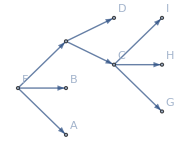

```mathematica
TreeToGraph[tree,ImageSize->Small]
```

Select and copy the full output tree and use it as input. Make sure, that you select the whole expression.

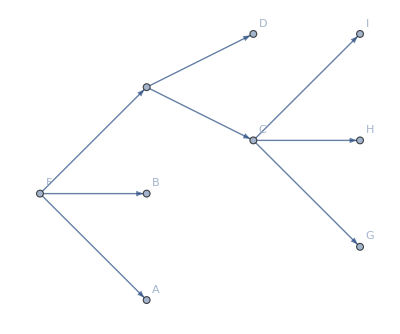

```mathematica
TreeToGraph[Tree["F",{"A","B",Tree[1,{Tree["C",{"G","H","I"}],"D"}]}]]
```

Extract all vertex names or just leaf or internal nodes.

```mathematica
{VertexList[tree],LeafList@tree,NodeList[tree]}
```

{{F,A,B,1,C,G,H,I,D},{A,B,G,H,I,D},{F,1,C}}

Query the branch lengths of all vertices, or for a selected set.

```mathematica
{BranchLength[tree],BranchLength[tree,{"F","B","C"}]}
```

{{1,0.1,0.2,0.5,0.3,0.1,0.2,0.3,0.4},{1,0.2,0.3}}

List vertices of subtrees.

```mathematica
{VertexList@Subtree[tree,"C"],VertexList@Subtree[tree,"A"],VertexList@Subtree[tree,"F"]}
```

{{C,G,H,I},{A},{F,A,B,1,C,G,H,I,D}}

EdgeList also works with Tree objects.

```mathematica
EdgeList[tree]
```

{F→A,F→B,F→1,1→C,1→D,C→G,C→H,C→I}

## Indices

DistanceIndex lists the absolute distance of each node from the ultimate root.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D:4;"]]
```

<|D→4,C→7,B→9,A→10|>

Note, that if no distance is specified for the root vertex (D), it is assumed to be 1.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D;"]]
```

<|D→1,C→4,B→6,A→7|>

Specify a base root by assigning a branch length of 0.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D:0;"]]
```

<|D→0,C→3,B→5,A→6|>

SubnodeIndex lists all the nodes below each node.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4):0.5)F:0.3;"];
SubnodeIndex[tree]
```

<|F→{A,B,1,C,G,H,I,D},1→{C,G,H,I,D},D→{},C→{G,H,I},I→{},H→{},G→{},B→{},A→{}|>

ChildIndex lists all the nodes immediately below each node.

```mathematica
ChildIndex[tree]
```

<|F→{A,B,1},1→{C,D},D→{},C→{G,H,I},I→{},H→{},G→{},B→{},A→{}|>

BranchLengthIndex lists the branch length values for each node (i.e. the distance of the node to its parent node).

```mathematica
BranchLengthIndex[tree]
```

<|F→0.3,A→0.1,B→0.2,1→0.5,C→0.3,G→0.1,H→0.2,I→0.3,D→0.4|>

## Layout

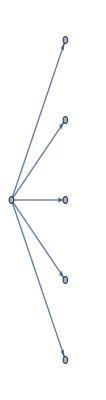
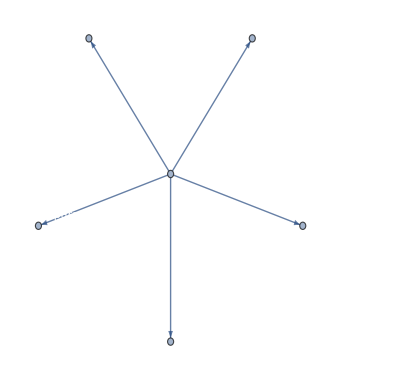
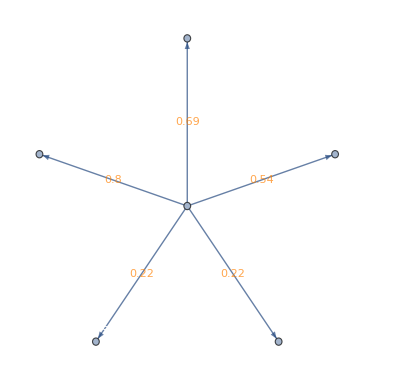
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tree=NewickToTree[PhylogeneticData["NewickSaccharomyces"]];
{
TreeToGraph[tree,VertexLabelStyle->White],
TreeToGraph[tree,VertexLabelStyle->White,GraphLayout->"RadialDrawing"],TreeToGraph[tree,EdgeLabels->Automatic,VertexLabelStyle->White,GraphLayout->{"StarEmbedding","Center"->Automatic},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Orange],
g=Cladogram[tree,EdgeLabels->Automatic,EdgeLabelStyle->Orange,ImagePadding->{{5,50},{5,10}}]
}
```

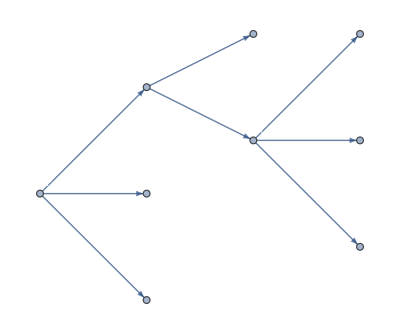
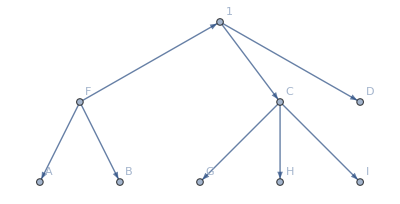
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
tree=NewickToTree[PhylogeneticData["ExampleNewick"]];
{
TreeToGraph[tree,VertexLabelStyle->White,ImagePadding->10],
TreeGraph[VertexList[tree],EdgeList[tree],VertexLabels->"Name"],
Cladogram[tree,EdgeLabels->Automatic,Frame->True,EdgeLabelStyle->Orange,LayerSizeFunction->(1#&),ImageSize->Medium]
}
```

A Cladogram is a directed graph, with directed edges.

```mathematica
DirectedGraphQ[Cladogram[tree]]
Cladogram[tree]//EdgeList
```

True

{F->A,F->B,F->1,1->C,1->D,C->G,C->H,C->I}

## Conversion to/from Newick format

Converting from Newick string to tree and back should yield the same string.

```mathematica
old="(((a,(,,),a3)b))d:1.4;";
new=TreeToNewick[NewickToTree[old]]
old===new
```

(((a,(,,),a3)b))d:1.4;

True

Unnamed and identical nodes are assigned unique indices to avoid collision.

```mathematica
tree=NewickToTree["((a,,b)a)"]
```

Tree[1,{Tree[a,{2,3,b}]}]

Nevertheless, labels are retained.

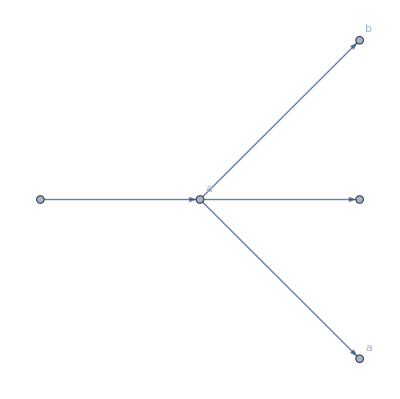

```mathematica
TreeToGraph[tree,ImageSize->Tiny]
```

## Conversion to/from hierarchical cluster format

Convert a hierarchical clustering structure to a tree.

```mathematica
cluster=PhylogeneticData["ExampleCluster1"]
tree=ClusterToTree[cluster]
```

Cluster[Cluster[Cluster[a,Cluster[h,j,1.52217,1,1],28.8538,1,2],Cluster[Cluster[c,e,10.1371,1,1],d,22.0063,2,1],47.1129,3,3],Cluster[Cluster[b,Cluster[g,i,2.5374,1,1],5.73533,1,2],f,13.6197,3,1],64.5168,6,4]

Tree[1,{Tree[2,{Tree[4,{a,Tree[7,{h,j}]}],Tree[5,{Tree[8,{c,e}],d}]}],Tree[3,{Tree[6,{b,Tree[9,{g,i}]}],f}]}]

A hierarchical clustering structure is always binary, therefore if it is converted to Tree, the result will always be strictly binary.

```mathematica
BinaryTreeQ[tree]
```

True

Visualize the tree.

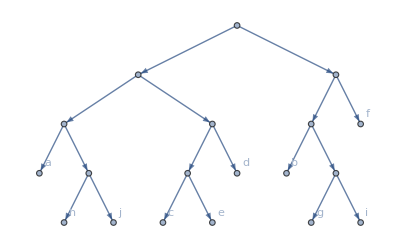
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{TreeToGraph[tree,GraphLayout->{"LayeredEmbedding",Orientation->Top}],
Cladogram[tree,Orientation->Top,ImageSize->Small,ImagePadding->10],
DendrogramPlot[cluster,Orientation->Top,LeafLabels->(Style[#,White]&),PlotStyle->White]}
```

Convert back to cluster format.

```mathematica
new=TreeToCluster[tree]
```

Cluster[Cluster[Cluster[a,Cluster[h,j,1.52217,1,1],28.8538,1,2],Cluster[Cluster[c,e,10.1371,1,1],d,22.0063,2,1],47.1129,3,3],Cluster[Cluster[b,Cluster[g,i,2.5374,1,1],5.73533,1,2],f,13.6197,3,1],64.5168,6,4]

Conversion from and to cluster format should result in the same tree up to numerical precision. Instead of SameQ, Equal should be used.

```mathematica
{cluster===new,cluster==new}
```

{False,True}

## Subtrees

Subtree returns the tree that is rooted at the requested node.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4):0.5)F;"]
Subtree[tree,"C"]
```

Tree[F,{A,B,Tree[1,{Tree[C,{G,H,I}],D}]}]

Tree[C,{G,H,I}]

If the vertex is a leaf, it is returned wrapped in Tree (with no branches), so that it can be converted to Graph more easily by other functions.

```mathematica
Subtree[tree,"H"]
```

Tree[H,{}]

If the vertex is not present in the tree, Missing[…] is returned.

```mathematica
Subtree[tree,"X"]
```

Missing[NotFound]

GraphHighlight works with Tree objects inside Cladogram, and not just with graphs, edges and vertices.

```mathematica
Cladogram[tree,GraphHighlight->Subtree[tree,#],PlotLabel->#,VertexLabels->"Name"]&/@{"F",1,"C","A"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Supertrees

Supertree returns the most compact subtree including all listed vertices.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4):0.5)F;"]
```

Tree[F,{A,B,Tree[1,{Tree[C,{G,H,I}],D}]}]

```mathematica
Supertree[tree,{"H","I"}]
```

Tree[C,{G,H,I}]

```mathematica
Supertree[tree,{"H","A","C"}]
```

Tree[F,{A,B,Tree[1,{Tree[C,{G,H,I}],D}]}]

Supertree works with any vertex, leaf or internal node.

```mathematica
Supertree[tree,"G"]
```

Tree[G,{}]

Visualize supertrees as highlighted subgraphs.

```mathematica
Cladogram[tree,ImageSize->Small,GraphHighlight->Supertree[tree,#],PlotLabel->#,VertexLabels->"Name"]&/@{"G",{"A","D"},{"H","I","C","D"}}
```

{-Graphics-,-Graphics-,-Graphics-}

## Paths and distances

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4):0.5)F;"];

list={{"I","F"},{"F","I"},{"H","H"},{"H","G"},{"G","D"},{"H","B"},{"C"},{"X"}};
path=TreePath[tree,#]&/@list;
dist=TreeDistance[tree,#]&/@list;

MapThread[Cladogram[tree,GraphHighlight->#1,ImageSize->Small,PlotLabel->Row@{#1,": ",#2}]&,{path,dist}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Clusters

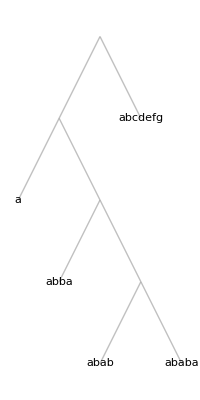
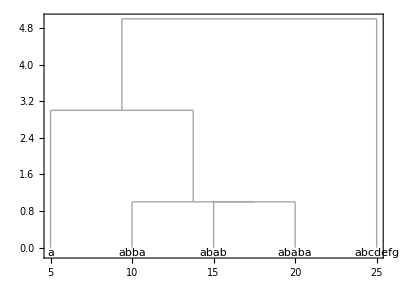
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
list={"a", "abba","abab", "ababa", "abcdefg"};
{
g=ClusteringTree[list,VertexLabelStyle->Black],
d=Dendrogram[list,Frame->True,PlotRangePadding->Scaled[.15]],
c=Cladogram[g,Orientation->Top,Frame->True,ImagePadding->All,PlotRangePadding->Scaled[.1],VertexLabelStyle->Black]
}
```

Since Cladogram measures distances from the root instead of (dis)similarity between vertices, the result is a mirrorred plot. To display it correctly, invert the vertex weights that represent the vertical absolute distance for each node.

```mathematica
w=PropertyValue[c,VertexWeight]
Cladogram[g,VertexWeight->(Max@w-w),Orientation->Top,Frame->True,ImagePadding->All,PlotRangePadding->Scaled[.1],VertexLabelStyle->Black,ImageSize->Small]
```

{5.,3.,0,1.,0,1.,0,0,0}

-Graphics-

## Graphs

Tree[1,{Tree[2,{Tree[4,{8}],5}],Tree[3,{6,7}]}]

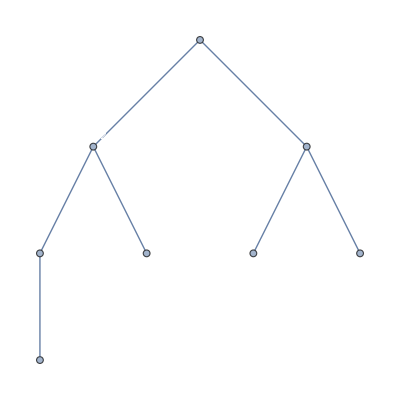
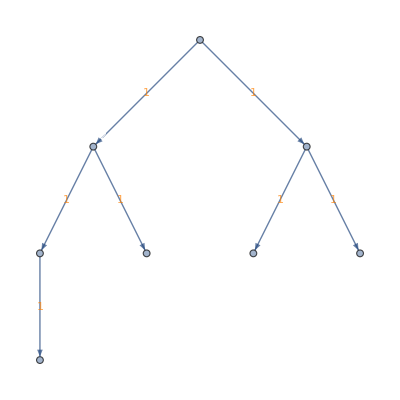
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
g=KaryTree[8,DirectedEdges->False,VertexLabels->"Index",VertexLabelStyle->White];
tree=GraphToTree[g]
{
g,
TreeToGraph[tree,VertexLabelStyle->White,GraphLayout->{"LayeredEmbedding","Orientation"->Top,"RootVertex"->1},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Orange],
Cladogram[tree,Orientation->Top,EdgeLabels->"EdgeWeight"],
Cladogram[g,Orientation->Top,EdgeLabels->"EdgeWeight"]
}
```

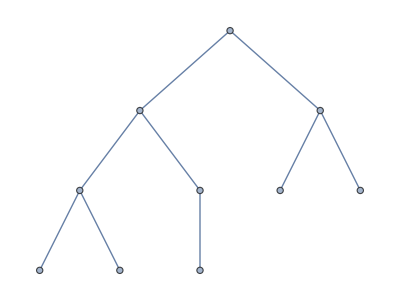
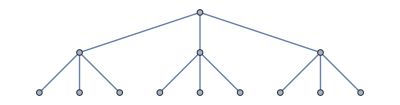
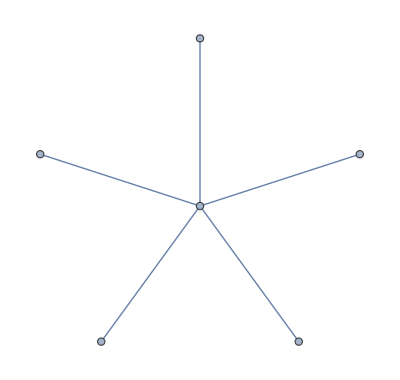
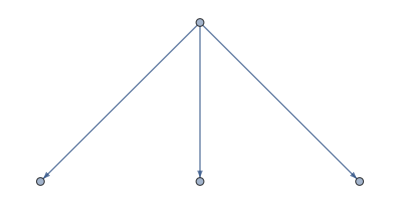

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graphs={KaryTree[10],CompleteKaryTree[3,3],StarGraph[6],TreeGraph[{1->2,1->3,1->4}]}
Cladogram[#,Orientation->Top]&/@graphs
```

## Phylogenetic data

Some example trees.

```mathematica
all=Most[PhylogeneticData["Names"]];
Cladogram[If[StringMatchQ[#,"*Newick*"],NewickToTree,ClusterToTree]@PhylogeneticData[#],ImageSize->Small,PlotLabel->#]&/@all
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A complex tree.

```mathematica
Cladogram[NewickToTree[PhylogeneticData["NewickEukarya"]],ImageSize->500,ImagePadding->{{1,100},{1,1}},LayerSizeFunction->(1/5#&),VertexSize->None,VertexLabelStyle->Directive[9,Italic]]
```

-Graphics-